# Finite difference quasireversible chronopotentiometry

## Fully explicit method

This notebook shows how a chronopotentiogram for the simple quasireversible reaction A + e ⇌ B can be simulated using explicit finite difference methods.

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[FindRoot::"cvnwt"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
xTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

yTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/2//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/2//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/10//N}]];

xTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];

yTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/2}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/2}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/10}]];
```

```mathematica
optionA={
PlotStyle-> {Red,AbsoluteThickness[0.5]},FrameTicks-> Automatic,
FrameLabel->{
Style["t",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],None,None}};
```

```mathematica
optionB={
PlotStyle-> {Red,AbsoluteThickness[0.5]},FrameTicks-> Automatic,
FrameLabel->{Style["lnτ^1/2 - 
StyleBox[\"t\",FontSlant->\"Italic\"]^1/2/
StyleBox[\"t\",FontSlant->\"Italic\"]^1/2",FontFamily-> "Times New Roman",FontColor-> Black,FontSize-> 12],Style["ℰ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],None,None}};
```

```mathematica
$Line=0;
```

## Set Up Solution

Use the method below to save memory. Only the surface concentration values are stored.

```mathematica
Clear[explicitChronoPot];

explicitChronoPot[m_Integer,n_Integer,d_,i_,ksDim_,α_]:=Module[{eValues,solveFor,iDim,conc,c},
conc=ConstantArray[{1.,0.},{m}];
iDim=(2*i)/(√(d*(n-1)));
solveFor[list_List]:=Module[{temp},
temp=ListCorrelate[{{d},{(1.-2.*d)},{d}},conc];
 conc=Partition[Flatten[{(iDim+4*temp⟦1,1⟧-temp⟦2,1⟧)/3,-(iDim-4*temp⟦1,2⟧+temp⟦2,2⟧)/3,temp,1.,0.}],2];
Take[conc,1]
];(*only the surface values are required*)

c=Rest@NestList[solveFor,conc,n-1];
c=Partition[Flatten[c],2];
eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c];
ℰ/.eValues;]
```

The iteration will continue and eventually produce negative concentrations. In real experiments the potential moves along to the potential of the next redox couple. To avoid the negative concentration we can put a condition on the simulation and stop when the concentrations become negative. This is conveniently done with NestWhileList.

```mathematica
Clear[explicitChronoPot2];

explicitChronoPot2[m_Integer,n_Integer,d_,i_,ksDim_,α_]:=Module[{eValues,solveFor,stopFor,iDim,conc,c},
conc=ConstantArray[{1.,0.},{m}];
iDim=(2*i)/(√(d*(n-1)));
stopFor[list_List]:=NonNegative[list[[1,1]]];

solveFor[list_List]:=Module[{temp},
temp=ListCorrelate[{{d},{(1.-2.*d)},{d}},conc];
 conc=Partition[Flatten[{(iDim+4*temp⟦1,1⟧-temp⟦2,1⟧)/3,-(iDim-4*temp⟦1,2⟧+temp⟦2,2⟧)/3,temp,1.,0.}],2];
Take[conc,1]
];

c=Rest@NestWhileList[solveFor,conc,stopFor,1,n-1,-1];
c=Partition[Flatten[c],2];
eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c];
ℰ/.eValues
]
```

The next method is for simulating current reversal experiments

```mathematica
Clear[explicitChronoPot3];

explicitChronoPot3[m_Integer,n_Integer,d_,i_,ksDim_,α_]:=Module[{solveFor,solveBack,stopFor,stopBack,c,eValues,conc,iDim,potentials1,potentials2},

conc=ConstantArray[{1.,0.},{m}];
iDim=(2*i)/(√(d*(n-1)));

stopFor[list_List]:=NonNegative[Part[list,1,1]];
stopBack[list_List]:=NonNegative[Part[list,1,2]];

solveFor[list_List]:=Module[{temp},
temp=ListCorrelate[{{d},{(1.-2.*d)},{d}},conc];
 conc=Partition[Flatten[{(iDim+4*temp⟦1,1⟧-temp⟦2,1⟧)/3,-(iDim-4*temp⟦1,2⟧+temp⟦2,2⟧)/3,temp,1.,0.}],2];
Take[conc,1]
];

c=Rest@NestWhileList[solveFor,conc,stopFor,1,n-1,-1];
c=Partition[Flatten[c],2];
eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c];
potentials1=ℰ/.eValues;

(*current reversal - stopping when the conc of R is zero*)
iDim=-iDim;
c=Rest@NestWhileList[solveFor,conc,stopBack,1,n-1,-1];
c=Partition[Flatten[c],2];
eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c];
potentials2=ℰ/.eValues;
Join[potentials1,potentials2]
]
```

## Set Parameter Values

### Set constants

```mathematica
Clear[F,R,T,f,𝒟,α];

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

f=F/(R*T);

𝒟=1.*^-5(*diffusion coefficient*);

α=0.5 (*transfer coefficient*);
```

### Simulation variables

```mathematica
Clear[ks,n,𝔻,m,i,ksDim];

i=-0.9;(*dimensionless current*)

ks=10.^6.;(*standard rate constant*)

n=401;

𝔻=0.35;

m=1+Ceiling[6*√(𝔻*(n-1))];

ksDim=ks*Sqrt[1./(𝒟*𝔻*(n-1))];(*dimensionless rate constant*)
```

## Solve it

```mathematica
potentials=explicitChronoPot2[m,n,𝔻,i,ksDim,α];//Timing
```

{0.234005,Null}

```mathematica
(*current reversal*)
potentials=explicitChronoPot3[m,n,𝔻,i,ksDim,α];//Timing
```

{0.295408,Null}

## Plot Potential v. Time

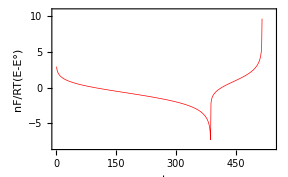

```mathematica
plot1=ListPlot[potentials,optionA,PlotRange:>  {{0,1.35*n}, {Min[potentials]-1, Max[potentials]+1}}]
```

The list of data potentials is a list of potentials at a given increment of time. We can add the coordinates of the time axis by defining the transition time to be one.

```mathematica
pot=Partition[Flatten[MapIndexed[{#1,#2/Length[potentials]}&,potentials]],2]//N;
```

Next step is to convert the data into a form that will enable us to do a log plot.

E=E^o'+RT/(2nF)ln D_R/D_O+RT/nF ln(τ^(1/2)-t^(1/2))/t^(1/2)

It's convenient to divide the data into the forward and reverse sections of the experiment.

```mathematica
potFor=Drop[Table[{Log[(1-Sqrt[pot⟦j,2⟧])/Sqrt[pot⟦j,2⟧]],pot⟦j,1⟧},{j,1,Length[potentials1]}],-1];

potRev=Drop[Table[{Log[(1-Sqrt[pot⟦j,2⟧])/Sqrt[pot⟦j,2⟧]],pot⟦j,1⟧},{j,Length[potentials1],Length[pot]}],-1];
potCombined=Join[potFor,potRev];
```

```mathematica
potPlot=ListPlot[potCombined,optionB]
```

We want to fit lines of best fit to the linear portions of this plot. This is done by selecting only the points that are in the linear region. We use Cases for this. In this example we search for all points on the initial part of the experiment, the "forward" part, with dimensionless potentials greater than 1.0, i.e. #⟦2⟧>1.0&.

```mathematica
Select[potRev,(-.05<#⟦2⟧<.05&)]
```

```mathematica
pot2=Cases[potFor,x_?(#⟦2⟧>1.0&)];

(*fit data to a linear curve*)
fitPot1=Fit[pot2,{1,x},x];

(*plot fitted data*)
fitPlot1=Plot[fitPot1,{x,Last[potFor]⟦1⟧,Max[pot2⟦Length[pot2],2⟧]},PlotStyle-> {Dashing[{0.01,0.01}]},DisplayFunction-> Identity];
```

We do the same for the current reversal part of the experiment In this example we search for all points on the reversal with dimensionless potentials greater than 2.5, i.e. #⟦1⟧>2.5&.

```mathematica
pot3=Cases[potRev,x_?(#⟦2⟧>2.5&)];

(*fit data to a linear curve*)
fitPot2=Fit[pot3,{1,x},x];

(*plot fitted data*)
fitPlot2=Plot[fitPot2,{x,Min[pot3⟦Length[pot3],1⟧],fitPot2⟦1⟧+1},PlotStyle->{Dashing[{0.01,0.01}]}];
```

```mathematica
Show[potPlot,fitPlot2,fitPlot1]
```

```mathematica
dtdE=Table[{potentials⟦j⟧,2/(potentials⟦j+1⟧-potentials⟦j-1⟧)},{j,2,Length[potentials]-1}];

ListPlot[dtdE]
```

The maximum of the derivative plot occurs at a dimensionless potential of -ln 2.

```mathematica
Select[dtdE,#⟦2⟧== Min[dtdE]&]
```

```mathematica
Minus[Log[2]//N]
```